```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 269 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
Clear[q]
q = { y1[t] , y2[t] }
```

{y1[t],y2[t]}

```mathematica
Clear[T]
T = 1/2( 2  m)  y1'[t]^2 + 1/2 m y2'[t]^2
```

m y1'[t]^2+1/2 m y2'[t]^2

```mathematica
Clear[V1]
V1 = - ( 2 m ) g y1[t] + 1/2 k ( y1[t] - l1 )^2
```

-2 g m y1[t]+1/2 k (-l1+y1[t])^2

```mathematica
Clear[V2]
V2 = - m g y2[t] + 1/2 k ( y2[t]-y1[t] - l2 )^2
```

-g m y2[t]+1/2 k (-l2-y1[t]+y2[t])^2

```mathematica
Clear[V]
V = V1 + V2
```

-2 g m y1[t]+1/2 k (-l1+y1[t])^2-g m y2[t]+1/2 k (-l2-y1[t]+y2[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ // pdConv
```

2 g m y1(t)+g m y2(t)-1/2 k (y1(t)-l1)^2-1/2 k (-l2-y1(t)+y2(t))^2+m ((∂y1(t))/(∂t))^2+1/2 m ((∂y2(t))/(∂t))^2

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ]  // Expand  
D[ D[ ℒ , D[q[[2]], t] ], t ]  - D[ ℒ , q[[2]] ]
```

-k l1+k l2-2 g m+2 k y1[t]-k y2[t]+2 m y1''[t]

-g m+k (-l2-y1[t]+y2[t])+m y2''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ]  - D[ ℒ , q[[i]] ] == 0 , 
{ i, 1, 2 } ] // Expand // TableForm
```

-k l1+k l2-2 g m+2 k y1[t]-k y2[t]+2 m y1''[t]==0
-k l2-g m-k y1[t]+k y2[t]+m y2''[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

k l1-k l2+2 g m-2 k y1[t]+k y2[t]-2 m y1''[t]==0
k l2+g m+k y1[t]-k y2[t]-m y2''[t]==0

```mathematica
Clear[parameters]
parameters = { 
k-> 200 , 
g-> 9.8 , 
m-> 10 , 
l1 -> 0.5 , 
l2 -> 0.75 } ;
parameters // TableForm
```

k→200
g→9.8
m→10
l1→0.5
l2→0.75

```mathematica
eqs /. parameters // TableForm
```

146.-400 y1[t]+200 y2[t]-20 y1''[t]==0
248.+200 y1[t]-200 y2[t]-10 y2''[t]==0

```mathematica
Clear[ics]
ics = { 
y1[0] == 0.75 , 
y1'[0] == 0 ,
y2[0] == 0.6  ,
y2'[0] == 0 } ;
ics // TableForm
```

y1[0]==0.75
y1'[0]==0
y2[0]==0.6
y2'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{y1[t]→InterpolatingFunction[…][t],y2[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 10 }, PlotLabels-> q  ]
```

-Graphics-

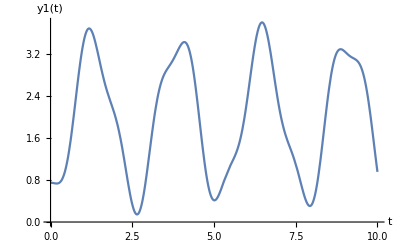

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```

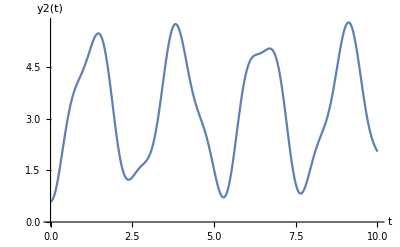

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[2]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 ,100 , 0.5  } ]
```